## Figure 1

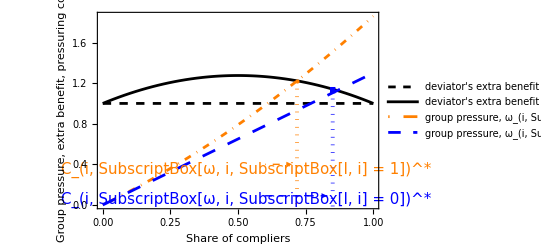

```mathematica
Show[Plot[{1, 1+1.1(x(1-x)), 1.3 x +0.7 *0.8*x^2  , 1.3 x +0.7 *0*x^2  },{x,0,1},PlotStyle->{Directive[ Black,Dashing[0.015]],Directive[Black, Tiny],Directive[ Orange,DotDashed], Directive[ Blue,Dashing[0.025]] } ,AspectRatio->1/GoldenRatio,Frame->True, FrameLabel->{{"Group pressure, extra benefit, pressuring costs",None},{"Share of compliers",None}},PlotLegends->{"deviator's extra benefit",
"deviator's extra benefit + ϑ_i", "group pressure, ω_(i, SubscriptBox[I, i] = 0)","group pressure, ω_(i, SubscriptBox[I, i] = 1)"}],Graphics[{{Dotted,Orange,Thickness[0.007],Line[{{0.718,1.22},{0.718,-0.13}}]},{Dotted,Blue,Thickness[0.007],Line[{{0.85,1.122},{0.85,-0.13}}]},Text[Style["C_(i, SubscriptBox[ω, i, SubscriptBox[I, i] = 1])^*",15,Orange],{0.53,0.35}]  ,{PointSize[Large],Orange,Point[{0.718,1.22}]},
{Blue,Rectangle[{0.84,1.1},{0.86,1.162}]},  
{DotDashed , Orange, Arrow[{{0.60,0.40},{0.7,0.40}}]},{Dashed , Blue, Arrow[{{0.6,0.09},{0.83,0.09}}]},
Text[Style["C_(i, SubscriptBox[ω, i, SubscriptBox[I, i] = 0])^*",15,Blue],{0.53,0.05}] }],PlotRangeClipping->False]
```

### Figure 2

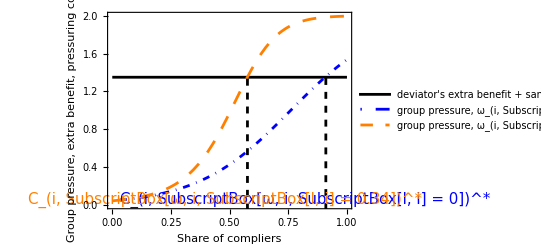

```mathematica
Show[Plot[{1+0.35, 2/(1+10*Exp[-5*(x-(0.3-0*x^2))]),2/(1+10*Exp[-5*(x-(0.3-1*x^2))])},{x,0,1},PlotStyle->{Directive[Black, Tiny],Directive[ Blue,DotDashed],Directive[ Orange,Dashing[0.025]] } ,AspectRatio->1/GoldenRatio,Frame->True, FrameLabel->{{"Group pressure, extra benefit, pressuring costs",None},{"Share of compliers",None}},PlotLegends->{
"deviator's extra benefit 
+ sanctioning costs υ_i", "group pressure, ω_(i, SubscriptBox[I, i] = 0)","group pressure, ω_(i, SubscriptBox[I, i] = 0.34)"}],
Graphics[{{Dashed,Black,Thickness[0.005],Line[{{0.91,1.342},{0.91,-0.111}}]},{Dashed,Black,Thickness[0.005],Line[{{0.576,1.334},{0.576,-0.111}}]},Text[Style["C_(i, SubscriptBox[ω, i, SubscriptBox[I, i] = 0])^*",15,Blue],{0.82,0.05}]  ,

(*{Dashed , Blue, Arrow[{{0.92,1.29},{1,1.29}}]},{Dashed , Blue, Arrow[{{0.84,1.29},{0.75,1.29}}]},{Dashed , Orange, Arrow[{{0.39,0.6},{0.29,0.6}}]},{Dashed , Orange, Arrow[{{0.44,0.6},{0.53,0.6}}]},*)
Text[Style["C_(i, SubscriptBox[ω, i, SubscriptBox[I, i] = 0.34])^*",15,Orange],{0.48,0.05}] }],PlotRangeClipping->True]
```

## Figure 2 ContourPlot

```mathematica
Manipulate[ContourPlot[K/(1+Subscript[β, 1]*(Exp[-Subscript[β, 2](c-(Subscript[β, 3]-Id))]))-1 -g(υ0-υ1*c +υ2*(1-c)*c), {c,0,1.1},{Id,0,1},FrameLabel-> {"Share of compliers","Indirect  moral  ties"},ContourLabels -> True,Epilog->First[Plot[Labeled[c^2,"c^2" , 0.75
],{c,0,1},PlotStyle->{Red,Dashed}]]], {{Subscript[β, 1],10},0,100},{{Subscript[β, 2],5},0,40,1},{{Subscript[β, 3],0.3},0,1},{{υ0, 0.35}, 0.01, 10, 0.5},{{υ1,0},0,8,0.1},{{υ2,0},0,20,0.2},{{K,2},0,5},{{g, 1}, 0, 20, 0.1}]
```

### Figure 3

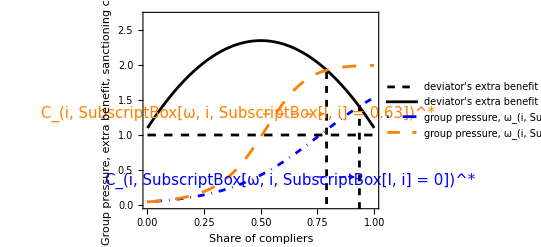

```mathematica
Show[Plot[{1, (1+0.1+5.0*x(1-x)), 2/(1+10*Exp[-5*(x-(0.3-0*x^2))]),2/(1+10*Exp[-5*(x-(0.3-x^2))])},{x,0,1},PlotRange-> {{0,1}{0,2.7}},PlotStyle->{Directive[ Black,Dashing[0.015]],Directive[Black, Tiny],Directive[ Blue,DotDashed], Directive[ Orange,Dashing[0.025]] } ,AspectRatio->1/GoldenRatio,Frame->True, FrameLabel->{{"Group pressure, extra benefit, sanctioning costs",None},{"Share of compliers",None}},PlotLegends->{"deviator's extra benefit",
"deviator's extra benefit + υ_i", "group pressure, ω_(i, SubscriptBox[I, i] = 0)","group pressure, ω_(i, SubscriptBox[I, i] =  .63)"}],Graphics[{{Dashed,Black,Thickness[0.005],Line[{{0.79,1.9},{0.79,-0.111}}]},{Dashed,Black,Thickness[0.005],Line[{{0.935,1.43},{0.935,-0.111}}]},Text[Style["C_(i, SubscriptBox[ω, i, SubscriptBox[I, i] = 0])^*",15,Blue],{0.63,0.35}]  ,
{DotDashed , Blue, Arrow[{{0.716,0.40},{0.915,0.40}}]},{Dashed , Orange, Arrow[{{0.51,1.3},{0.78, 1.3}}]},
Text[Style["C_(i, SubscriptBox[ω, i, SubscriptBox[I, i] = 0.63])^*",15,Orange],{0.4,1.3}] }],PlotRangeClipping->False]
```

## Figure C1 ContourPlot

```mathematica
Manipulate[ContourPlot[K/(1+Subscript[β, 1]*(Exp[-Subscript[β, 2](c-(Subscript[β, 3]-Id))]))-1 -g(υ0-υ1*c +υ2*(1-c)*c), {c,0,1.1},{Id,0,1},FrameLabel-> {"Share of compliers","Indirect  moral  ties"},ContourLabels -> True,Epilog->First[Plot[Labeled[c^2,"c^2" , 0.68
],{c,0,1},PlotStyle->{Red,Dashed}]]], {{Subscript[β, 1],10},0,100},{{Subscript[β, 2],5},0,40,1},{{Subscript[β, 3],0.3},0,1},{{υ0, 0.1}, 0.00, 10, 0.5},{{υ1,0},0,8,0.1},{{υ2,5},0,20,0.2},{{K,2},0,5},{{g, 1}, 0, 20, 0.1}]
```

## Figure C2

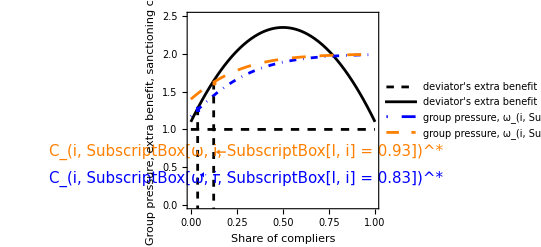

```mathematica
Show[Plot[{1, (1+0.1+5*x(1-x)), 2/(1+10*Exp[-5*(x-(0.3-0.83))]),2/(1+10*Exp[-5*(x-(0.3-0.93))])},{x,0,1.0},PlotRange->{{0,1}{0,2.5}},PlotStyle->{Directive[ Black,Dashing[0.015]],Directive[Black, Tiny],Directive[ Blue,DotDashed], Directive[ Orange,Dashing[0.025]] } ,AspectRatio->1/GoldenRatio,Frame->True, FrameLabel->{{"Group pressure, extra benefit, sanctioning costs",None},{"Share of compliers",None}},PlotLegends->{"deviator's extra benefit",
"deviator's extra benefit + υ_i", "group pressure, ω_(i, SubscriptBox[I, i] = 0.83)","group pressure, ω_(i, SubscriptBox[I, i] = 0.93)"}],Graphics[{{Dashed,Black,Thickness[0.005],Line[{{0.037,1.28},{0.037,-0.111}}]},{Dashed,Black,Thickness[0.005],Line[{{0.124,1.62},{0.124,-0.111}}]},Text[Style["C_(i, SubscriptBox[ω, i, SubscriptBox[I, i] = 0.83])^*",15,Blue],{0.3,0.35}]  ,{PointSize[Large],Orange,Point[{0.124,1.62}]},
{Blue,Rectangle[{0.028,1.23},{0.05,1.3}]},
{DotDashed , Blue, Arrow[{{0.2,0.40},{0.05,0.40}}]},{Dashed , Orange, Arrow[{{0.19,0.7},{0.135,0.7}}]},
Text[Style["C_(i, SubscriptBox[ω, i, SubscriptBox[I, i] = 0.93])^*",15,Orange],{0.3,0.7}] }],PlotRangeClipping->False]
```

### Figure D1

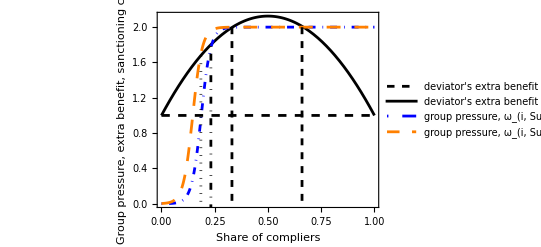

```mathematica
Show[Plot[{1, (1+4.5*x(1-x)), 2/(1+50*Exp[-45*(x-(0.1-0*x^2))]),2/(1+50*Exp[-45*(x-(0.1-0.04))])},{x,0,1},PlotStyle->{Directive[ Black,Dashing[0.015]],Directive[Black, Tiny],Directive[ Blue,DotDashed], Directive[ Orange,Dashing[0.025]] } ,AspectRatio->1/GoldenRatio,Frame->True, FrameLabel->{{"Group pressure, extra benefit, sanctioning costs",None},{"Share of compliers",None}},PlotLegends->{"deviator's extra benefit",
"deviator's extra benefit + υ_i", "group pressure, ω_(i, SubscriptBox[I, i] = 0)","group pressure, ω_(i, SubscriptBox[I, i] = 0.04)"}],Graphics[{{Dashed,Black,Thickness[0.005],Line[{{0.66,1.999},{0.66,-0.111}}]},{Dashed,Black,Thickness[0.005],Line[{{0.331,1.999},{0.331,-0.111}}]},{DotDashed,Black,Thickness[0.005],Line[{{0.232,1.786},{0.232,-0.111}}]},{Dotted,Black,Thickness[0.005],Line[{{0.185,1.676},{0.185,-0.111}}]},
Text[Style["C_(i, SubscriptBox[ω, i, SubscriptBox[I, i] = 0.0])^*",10,Blue],{0.28,-0.39}]  ,
Text[Style["C_(i, SubscriptBox[ω, i, SubscriptBox[I, i] = 0.04])^*",10,Orange],{0.12,-0.39}] }],PlotRangeClipping->False]
```

### Figure C3 ContourPlot

```mathematica
Manipulate[ContourPlot[K/(1+Subscript[β, 1]*(Exp[-Subscript[β, 2](c-(Subscript[β, 3]-Id))]))-1 -g(υ0-υ1*c +υ2*(1-c)*c), {c,0,1.1},{Id,0,1},FrameLabel-> {"Share of compliers","Indirect  moral  ties"},ContourLabels -> True, Epilog->First[Plot[Labeled[c^2,"c^2" , 0.63
],{c,0,1},PlotStyle->{Red,Dashed}]]], {{Subscript[β, 1],10},0,100,2},{{Subscript[β, 2],7.5},0,40,1},{{Subscript[β, 3],0.2},0,1},{{υ0, 1}, 0.00, 10, 0.5},{{υ1,-2},-10,10,0.1},{{υ2,-7},-10,20,0.2},{{K,2},0,5},{{g, 1}, 0, 20, 0.1}]
```

## Figure C4

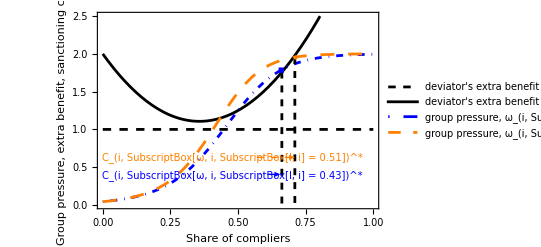

```mathematica
Show[Plot[{1,1+(1+2x -7*(1-x)x), 2/(1+10*Exp[-7.5*(x-(0.2-0.3*x^2))]),2/(1+10*Exp[-7.5*(x-(0.2-0.6*x^2))])},{x,0,1},PlotRange->{{0,1}{0,2.5}},PlotStyle->{Directive[ Black,Dashing[0.015]],Directive[Black, Tiny],Directive[ Blue,DotDashed], Directive[ Orange,Dashing[0.025]] } ,AspectRatio->1/GoldenRatio,Frame->True, FrameLabel->{{"Group pressure, extra benefit, sanctioning costs",None},{"Share of compliers",None}},PlotLegends->{"deviator's extra benefit",
"deviator's extra benefit + υ_i", "group pressure, ω_(i, SubscriptBox[I, i] = 0.43)","group pressure, ω_(i, SubscriptBox[I, i] = 0.51)"}],Graphics[{{Dashed,Black,Thickness[0.005],Line[{{0.71,1.957},{0.71,0}}]},{Dashed,Black,Thickness[0.005],Line[{{0.662,1.766},{0.662,0}}]},{PointSize[Large],Orange,Point[{0.71,1.96}]},
{Blue,Rectangle[{0.65,1.75},{0.67,1.82}]},{DotDashed , Blue, Arrow[{{0.58,0.405},{0.656,0.405}}]},{Dashed , Orange, Arrow[{{0.57,0.63},{0.71,0.63}}]},
Text[Style["C_(i, SubscriptBox[ω, i, SubscriptBox[I, i] = 0.43])^*",10,Blue],{0.48,0.39}]  ,
Text[Style["C_(i, SubscriptBox[ω, i, SubscriptBox[I, i] = 0.51])^*",10,Orange],{0.48,0.63}] }],PlotRangeClipping->False]
```